```mathematica
ClearAll["Global`*"]
```

```mathematica
ST[vv_,n_]:= Mod[n,vv]-Mod[(n-1),vv]

LAdd[vv_,n_] := Sum[ vv^k/k,{k,1,Log[vv,n]}]
E1[vv_,n_,0]:=1
E1[vv_,n_,k_] := E1[vv,n,k] = Sum[ ST[vv, j] E1[vv,Floor[n/j],k-1],{j,1,n}]
E2[vv_,n_,k_] := E2[vv,n,k] = Sum[ (-1)^(k-j) Binomial[k,j] E1[vv,n,j],{j,0,k}]
e2[vv_,n_,k_] := e2[vv,n,k] = E2[vv,n,k]-E2[vv,n-1,k]
P2[vv_,n_] := Sum[ (-1)^(k+1)/k E2[vv,n,k],{k,1,Log[2,n]}]
p2[vv_,n_] := n+Sum[ (-1)^(k+1)/k e2[vv,n,k],{k,1,Log[2,n]}]
P2a[n_] := P2a[n]=Sum[ p2[j,j],{j,2,n}]
md[x_, y_] := y/2 - y/Pi Sum[ Sin[ 2 Pi k x / y ]/k,{k,1,200}]
md2[x_, y_] := (y/2 - y/Pi Sum[ Sin[ 2 Pi k x / y ]/k,{k,1,200}])-(y/2 - y/Pi Sum[ Sin[ 2 Pi k (x-1) / y ]/k,{k,1,200}])
md3[x_, y_] := (y/2 - y/Pi Sum[ Sin[ 2 Pi k x / y ]/k,{k,1,1000}])-(y/2 - y/Pi Sum[ Sin[ 2 Pi k (x-1) / y ]/k,{k,1,1000}])
```

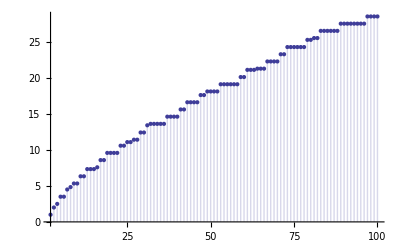

```mathematica
DiscretePlot[P2[5,n]+LAdd[5,n],{n,2,100}]
```

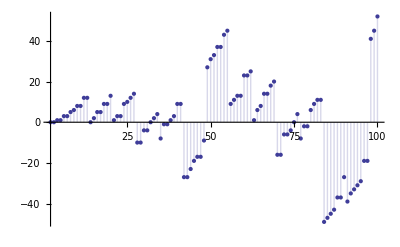

```mathematica
DiscretePlot[{E2[7,n,2]},{n,2,100}]
```

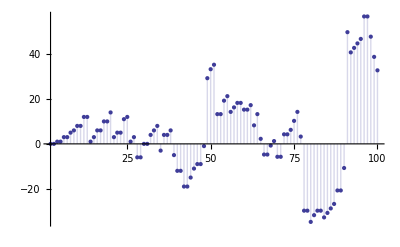

```mathematica
DiscretePlot[{E2[13/2,n,2]},{n,2,100}]
```

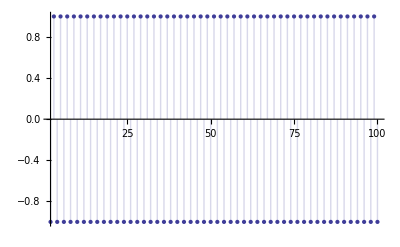

```mathematica
DiscretePlot[{E2[2,n,1]-E2[2,n-1,1]},{n,2,100}]
```

```mathematica
N[md2[100,6]]
```

0.997257

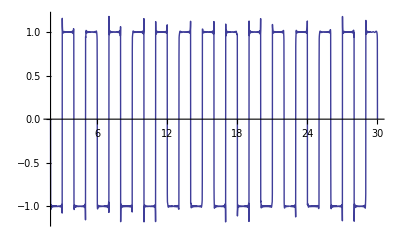

```mathematica
Plot[ md2[n,2],{n,2,30}]
```

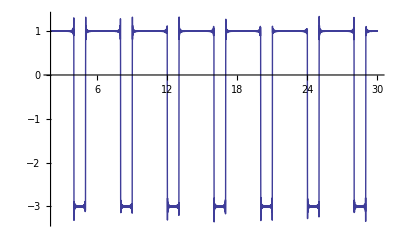

```mathematica
Plot[ md2[n,4],{n,2,30}]
```

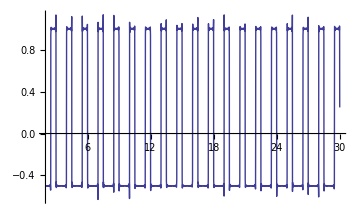

```mathematica
Plot[ md2[n,3/2],{n,2,30}]
```

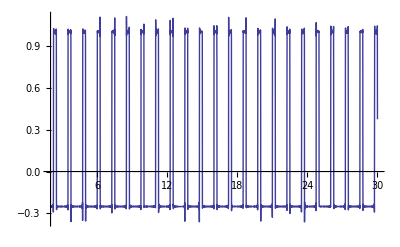

```mathematica
Plot[ md2[n,5/4],{n,2,30}]
```

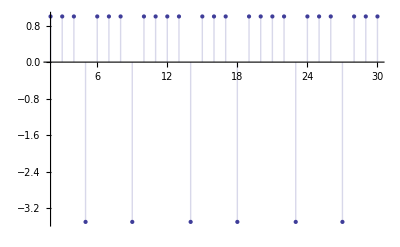

```mathematica
DiscretePlot[{E2[9/2,n,1]-E2[9/2,n-1,1]},{n,2,30}]
```

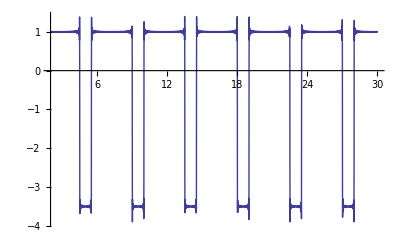

```mathematica
Plot[ md2[n,9/2],{n,2,30}]
```

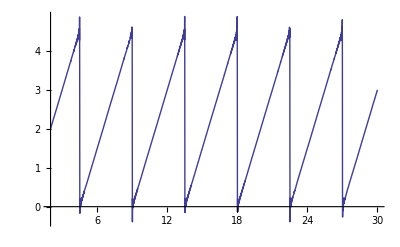

```mathematica
Plot[ md[n,9/2],{n,2,30}]
```

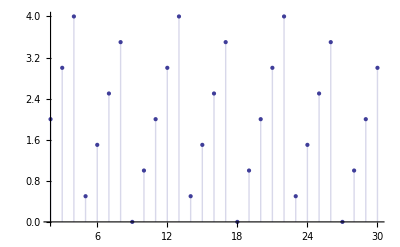

```mathematica
DiscretePlot[Mod[n,9/2],{n,2,30}]
```

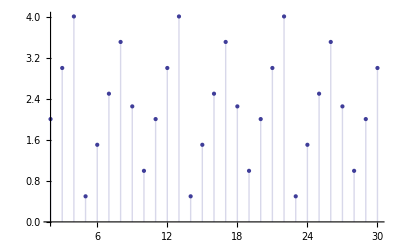

```mathematica
DiscretePlot[ md[n,9/2],{n,2,30}]
```

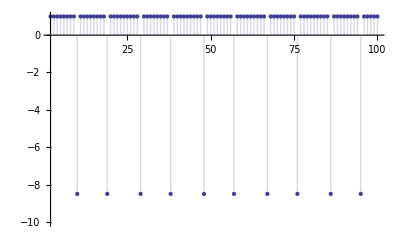

```mathematica
DiscretePlot[ST[9.5,n],{n,2,100}, PlotRange->{{2,100},{-10,1}}]
```

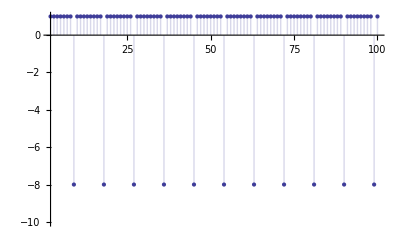

```mathematica
DiscretePlot[ST[9,n],{n,2,100}, PlotRange->{{2,100},{-10,1}}]
```

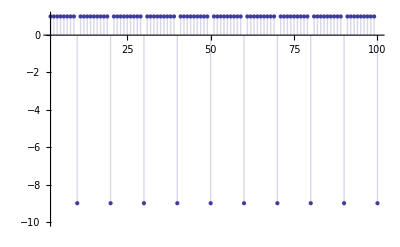

```mathematica
DiscretePlot[ST[10,n],{n,2,100}, PlotRange->{{2,100},{-10,1}}]
```

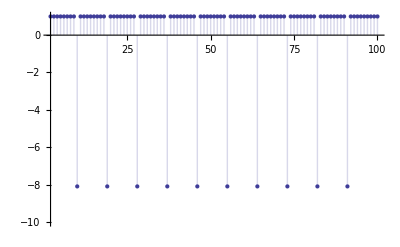

```mathematica
DiscretePlot[ST[9.1,n],{n,2,100}, PlotRange->{{2,100},{-10,1}}]
```

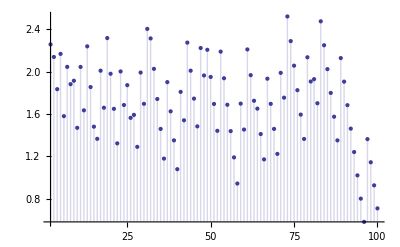

```mathematica
DiscretePlot[P2[2,n]+LAdd[2,n]-LAdd[1.00001,n]+LAdd[1.000001,1.4513692],{n,2,100}]
```

```mathematica
LogIntegral[1.000001]
```

-13.2383

```mathematica
LAdd[1.000001,80]-LAdd[1.000001,1.4513692]
```

25.6786-2.49006×10^-10 ⅈ

```mathematica
N[LogIntegral[80]]
```

25.6786

```mathematica
LAdd[1.000001,1.4513692]
```

13.8155

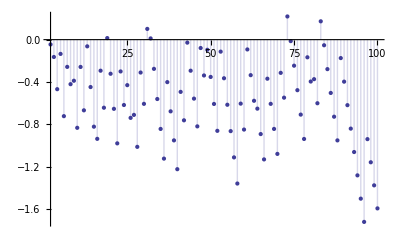

```mathematica
DiscretePlot[P2[2,n]+LAdd[2,n] -LogIntegral[n],{n,2,100}]
```

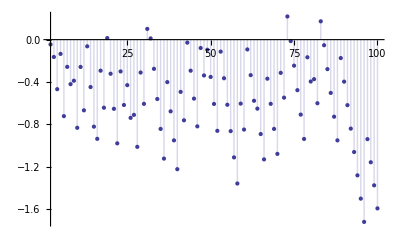

```mathematica
DiscretePlot[P2[2,n]+LAdd[2,n]-LAdd[1.00001,n]+LAdd[1.00001,1.4513692],{n,2,100}]
```

```mathematica
s1[n_] := Sum[ Co[k],{k,1,n}]
s2[n_] := Sum[ ST[5/2,k],{k,1,n}]
```

```mathematica
s1[100]
```

0

```mathematica
s2[100]
```

0

```mathematica
Co[2]
```

-1/4

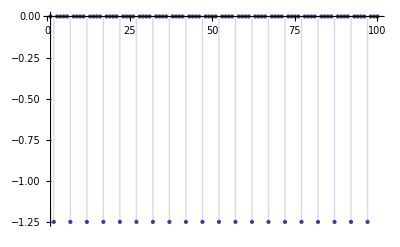

```mathematica
DiscretePlot[ { s1[n]-s2[n]},{n,1,100}]
```

```mathematica
DiscretePlot[ { s2[n]},{n,1,100}]
```

```mathematica
s1[1]
```

1

```mathematica
Table[ {n,s1[n],s2[n]},{n,1,40}]//TableForm
```

1 | 1 | 1
2 | 3/4 | 2
3 | 1/2 | 1/2
4 | 3/2 | 3/2
5 | 0 | 0
6 | 1 | 1
7 | 3/4 | 2
8 | 1/2 | 1/2
9 | 3/2 | 3/2
10 | 0 | 0
11 | 1 | 1
12 | 3/4 | 2
13 | 1/2 | 1/2
14 | 3/2 | 3/2
15 | 0 | 0
16 | 1 | 1
17 | 3/4 | 2
18 | 1/2 | 1/2
19 | 3/2 | 3/2
20 | 0 | 0
21 | 1 | 1
22 | 3/4 | 2
23 | 1/2 | 1/2
24 | 3/2 | 3/2
25 | 0 | 0
26 | 1 | 1
27 | 3/4 | 2
28 | 1/2 | 1/2
29 | 3/2 | 3/2
30 | 0 | 0
31 | 1 | 1
32 | 3/4 | 2
33 | 1/2 | 1/2
34 | 3/2 | 3/2
35 | 0 | 0
36 | 1 | 1
37 | 3/4 | 2
38 | 1/2 | 1/2
39 | 3/2 | 3/2
40 | 0 | 0

```mathematica
ST[5/2,1]
```

1

```mathematica
S
```

```mathematica
ST[5/2,2]
```

1

```mathematica
ST[5/2,3]
```

-3/2

```mathematica
ST[5/2,4]
```

1

```mathematica
ST[5/2,5]
```

-3/2

```mathematica
p2[2,2]
```

-1

```mathematica
p2[3,3]
```

-2

```mathematica
p2[4,4]
```

-7/2

```mathematica
p2[5,5]
```

-4

```mathematica
p2[6,6]
```

-6

```mathematica
p2[7,7]
```

-6

```mathematica
p2[8,8]
```

-23/3

```mathematica
p2[9,9]
```

-17/2

```mathematica
p2[10,10]
```

-10

```mathematica
P2a[100]
```

-75307/15

```mathematica
ex[n_] := n(n+1)/2
```

```mathematica
5050
```

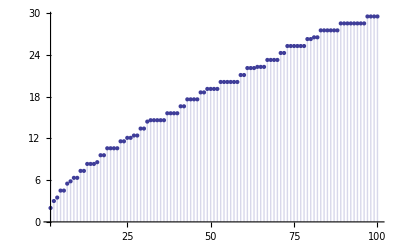

```mathematica
DiscretePlot[ P2a[n],{n,2,100}]
```

```mathematica
p2[2]
```

```mathematica
Table[ {n, p2[n,n]},{n,2,100}]//TableForm
```

2 | 1
3 | 1
4 | 1/2
5 | 1
6 | 0
7 | 1
8 | 1/3
9 | 1/2
10 | 0
11 | 1
12 | 0
13 | 1
14 | 0
15 | 0
16 | 1/4
17 | 1
18 | 0
19 | 1
20 | 0
21 | 0
22 | 0
23 | 1
24 | 0
25 | 1/2
26 | 0
27 | 1/3
28 | 0
29 | 1
30 | 0
31 | 1
32 | 1/5
33 | 0
34 | 0
35 | 0
36 | 0
37 | 1
38 | 0
39 | 0
40 | 0
41 | 1
42 | 0
43 | 1
44 | 0
45 | 0
46 | 0
47 | 1
48 | 0
49 | 1/2
50 | 0
51 | 0
52 | 0
53 | 1
54 | 0
55 | 0
56 | 0
57 | 0
58 | 0
59 | 1
60 | 0
61 | 1
62 | 0
63 | 0
64 | 1/6
65 | 0
66 | 0
67 | 1
68 | 0
69 | 0
70 | 0
71 | 1
72 | 0
73 | 1
74 | 0
75 | 0
76 | 0
77 | 0
78 | 0
79 | 1
80 | 0
81 | 1/4
82 | 0
83 | 1
84 | 0
85 | 0
86 | 0
87 | 0
88 | 0
89 | 1
90 | 0
91 | 0
92 | 0
93 | 0
94 | 0
95 | 0
96 | 0
97 | 1
98 | 0
99 | 0
100 | 0